# SurfCalc for raft on MF03 fixture - no balls - for abs hgt .

PZ Takacs

## SurfCalc raft on MF03 abs hgt 02.nb

2015.02.15 - Added output section for equations from repeatability runs and readin of eqn files.
2015.02.13 - Added Import for 3ball cal file datum plane equations, correcting the raft plane for absolute height wrt 3ball datum.
2015.02.04 - Raft on MF03 with fiducial surfs for abs height.
2014.12.12 - from SurfCalc OGP_CCDonMF01 ver4.nb. Customized for commissioning the MF03 holddown fixture. Added ball sphere fitting section.

Requires that the fixture be mounted on the OGP machine with the 2 LL and LR balls along the lower edge and the single UC ball at the rear. The origin of the coordinate system is set to the scribe marks on the front (larger) fiducial surface in the LL corner. The x-axis angle is set with the scribe mark on the right side of the front fiducial surface. All measurements are made relative to this system.

Eventually the ball centers will define the datums.

```mathematica
Button["Run Initialization first",SetOptions[Button,Background->LightOrange];FrontEndExecute[FrontEndToken["EvaluateInitialization"]]]
```

Run Initialization first

## 1. Initialize

Data and time of last saved modification. This is an Initialization cell that executes automatically whenever the nb is opened.

```mathematica
nb=EvaluationNotebook[]
```

jsafq_shm15FrontEndObject[LinkObject["jsafq_shm", 3, 1]]15SurfCalc raft on MF03 abs hgt 02.nb/Users/takacs/ Peter work f/Projects/LSST project/Analysis codes/SurfCalc raft on MF03 abs hgt 02.nb

```mathematica
SetOptions[Button,Background->LightOrange];
```

```mathematica
DateString["FileModificationTime"/.NotebookInformation[],TimeZone->0]
```

Sat 7 Mar 2015 07:12:31

```mathematica
hms$:=DateString[{"Hour","Minute","Second"}]
```

```mathematica
Off[General::"spell1"]
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
$SystemID
```

MacOSX-x86-64

```mathematica
$OperatingSystem
```

MacOSX

```mathematica
TS[x_]:=ToString[x]
```

#### Conversion factors to meters for numbers in the indicated units:

```mathematica
mm=10.^-3;
micron=10.^-6;
µm=10.^-6;
nm=10.^-9;
Angstroms=10.^-10;
micronsToAngstroms=10^4;
```

## 1.1. Define statistical functions for profile data. (Inactive)

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}]
```

MAKE SURE THE FOURIER OPTIONS ARE SET CORRECTLY EACH TIME THE FT IS DONE.

Define the biased stddev functiion. The built in StdDev fcn has n-1 in the denom. Change it to n.

Now compute std dev in different ways: The default StandardDeviation is the unbiased version, with n-1 in the denominator.

```mathematica
sdevBiased=.
```

```mathematica
sdevUnB[in_]:=N[StandardDeviation[in]]
```

```mathematica
sdevBiased[in_]:=StandardDeviation[in]Sqrt[(Length[in]-1)/Length[in]]
```

```mathematica
rmsBias[in_]:=Sqrt[Plus@@(in^2)/Length[in]]
```

Next is the RMS. Sum the squares, divide by N and then take the root. (Root of the Mean Square)

```mathematica
rmsrawbiased=.;
```

```mathematica
rms[in_]:=N[√((Plus@@((in)^2))/Length[in])]
```

See that one must subtract the mean from the input data first, before squaring, in order to compute the standard deviation correctly.

```mathematica
sdevBruteUnBiased[in_]:=N[√((Plus@@((in-Mean[in])^2))/(Length[in]-1))]
```

```mathematica
detrend[anylist_,order_Integer]:=Block[{npts,xlist,fitlist,x},
If[
order>=0,
xlist=Table[x^i,{i,0,order}];
		npts=Length[anylist];
		func=Fit[anylist,xlist,x];
		fitlist={};
		Do[AppendTo[fitlist,func],{x,1,npts}];
		Return[anylist-fitlist],
Return[anylist]
]
]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list.

```mathematica
psd1[in_,delx_]:=(SetOptions[Fourier,FourierParameters->{1,1}];
nPts=Length[in];
FTwork=Fourier[in];
psd2side=(2 delx/nPts) Abs[FTwork]^2;
psd1side=Drop[psd2side,-Floor[(nPts-1)/2]];
(*Apply bookkeeping factors to end terms*)
psd1side[[1]]=psd1side[[1]]/2; 
If[EvenQ[nPts],psd1side[[-1]]=psd1side[[-1]]/2,Null];
psd1side
)
```

```mathematica
npts=.
```

```mathematica
test11={1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
psd1[test11,1.]
```

{396.,69.2929,18.8168,9.62957,6.64709,5.6137}

```mathematica
nPts
```

11

```mathematica
Length[psd2side]
```

11

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list. NOTE: Need to know the length of the input z-vector for the ntot number. Can't get it from the length of the psd list. It should be the length of the psd2side list if this corresponds to the input psd list.

```mathematica
rmspsdIDX[psd_,nztot_,delx_,lo_,hi_]:=(rmsval=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];Print["RMS over index range [",lo,",",hi,"] = ",rmsval])
```

```mathematica
rmspsd[psd_,nztot_,delx_,lo_,hi_]:=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];
```

Now generalize the variance calculation to apply to zero-padded data to give the same result as for the original data set. Need to boost up each term separately.

```mathematica
varGen[anylist_,beforeLen_,afterLen_]:=N[sfac=afterLen/beforeLen;(sfac Plus@@(anylist^2))/afterLen-sfac^2 ((Plus@@anylist)/afterLen)^2]
```

```mathematica
sdevGen=√varGen[worklist,nbefore,nafter]
```

√(-(1. worklist^2)/nbefore^2+(2.+worklist)/nbefore)

#### Add a point digitizer to a plot. Results are put into vector "res".

```mathematica
locatePts[plotname_]:=
Block[ {}, 
res = {}; 
Dynamic[res]; 
  EventHandler[ 
         plotname, {"MouseDown" :>( AppendTo[res, MousePosition["Graphics"]])} 
        ] ]
```

#### The following tick function rescales the axes labels from the default [xmin, xmax] range by offsetting the starting point by b and scaling the tick value by m. Note that you need to specify the AxesOrigin in terms of the unshifted function.

```mathematica
$TextStyle={FontFamily->Arial,FontSize->10}
```

{FontFamily→Arial,FontSize→10}

```mathematica
Style[PlotLabel,DefaultOptions->{FontFamily->Arial}]
```

PlotLabel

```mathematica
tickf[min_,max_,m_,b_,step_]:= Table[{i,m (i-b)},{i,min,max,step}]
```

File name conventions

```mathematica
filename=.;filenamefull=.;fnames=.;plotname=.;filepath=.;filepathfull=.;
```

```mathematica
filein=.;fileinroot=.;fileinS=.;
```

## 2. Enter full file path here to set working directory:

Enter the filepath for a file in each of the data directories, then copy the desired path into the filepathfull expression.

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Raft runs 150204-05/FullRaftRun1.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150220/150220LPfidRaft01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150224/150224RaftAbsHgt05.DAT"
```

#### Execute following after selecting the proper file path.

```mathematica
filepathfull = "/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150220/150220LPfidRaft01.DAT";
```

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150220

Use the filename form appropriate for the computer platform, either MacOSX or Windows

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[$OperatingSystem=="Windows",sep$="\\",sep$="/"];
```

```mathematica
manualcalcFlag=False; (*set for automated analysis*)
```

```mathematica
manualcalcFlag=True; (*to stop automated analysis with default parameters*)
```

## 3. Read in OGP txt format. Contours. This is treated as FREEFORM data, i.e. no set nrows or ncols.

Data is in the form of a big list of triplets in units of mm. The X,Y coordinate is included with the z-value. Note that this is NOT a rectangular data array, so can't use the array plot functions unless the data is padded to make a grid, which is not possible with OGP freefom data.

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150220

```mathematica
datain=.;datain2=.;datainXYZSR=.;skipnum=.;nRows=.;nCols=.;delx=.; dely=.;(*nominal scan values *)
```

```mathematica
fnames=FileNames["*.DAT"];Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | 150220LPfidRaft01.DAT
2 | 150220LPfidRaft02.DAT
3 | 150220LPfidRaft03.DAT
4 | 150220 Raft#2 corners02.DAT
5 | 150220 Raft#2 corners03.DAT
6 | 150220 Raft#2 corners04.DAT
7 | 150220 Raft#2 corners05.DAT
8 | 150220 Raft#2 corners.DAT
9 | MF03 150220 LP ball cal run01.DAT
10 | MF03 150220 LP ball cal run02.DAT
11 | MF03 150220 VPfidLPballs01.DAT
12 | MF03 150220 VPfidLPballsRaft01.DAT
13 | MF03 150220 VPfidLPballsRaft02.DAT

#### Pick the OGP file from the list

```mathematica
inst$="OGP"
```

OGP

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Options[SelectionMove]
```

{AutoScroll→True}

```mathematica
2
```

2

```mathematica
nf=Input["Enter index of file desired",nf]
```

1

```mathematica
fileinfull =fnames[[nf]]
fileinroot=FileBaseName[fileinfull]
fileinS=fileinroot;filein=fileinS;
```

150220LPfidRaft01.DAT

150220LPfidRaft01

```mathematica
(*Read in raw data here*)
datain=Import[fileinfull,"Data"];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[manualcalcFlag,Interrupt[] ](* Stop here to execute next expressons individually as needed to clean up data *)
```

```mathematica
datain[[1;;20]]
```

{{C:\DATA\MF03,holddown\MF03,150220,LP,FidRaft.RTN,02/20/2015,16:50:16,4},{Point,1},{-0.001072,-0.001183,0.01101,mm},{},{Point,2},{0.317047,-0.23142,-0.001741,mm},{},{Point,3},{9.27016,-2.83987,0.010638,mm},{},{Contour,4},{9.3034,-2.61323,0.010422,mm},{9.27731,-2.61337,0.010447,mm},{9.25971,-2.61346,0.010017,mm},{9.22331,-2.61394,0.01058,mm},{9.20401,-2.61464,0.010368,mm},{9.17114,-2.61881,0.010316,mm},{9.15486,-2.62389,0.010648,mm},{9.12304,-2.63905,0.010519,mm},{9.10759,-2.64843,0.010782,mm}}

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
workdir=filein<>"_files"
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150220

150220LPfidRaft01_files

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

150220LPfidRaft01_files already exists. Using it for output.

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150220/150220LPfidRaft01_files

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Strip out all of the Contour record, nulls and EORs, making one long list of points.

```mathematica
Length[datain]
Count[datain,{}] (* Counts the number of blank records in the file*)
```

683

15

```mathematica
datain2=Select[datain,Length[#]>0&];(*Strip out the blank lines*)
```

```mathematica
contourPos=Position[datain2,"Contour",2]
Length[contourPos]
```

{{8,1},{92,1},{176,1},{260,1},{343,1},{424,1},{505,1},{587,1}}

8

Delete all of the Point points. Find all the locations where Point occurs. Form ppos2 by taking each positin and adding 1 to specify the data point values corresponding to the Point function. THen Delete the point pairs.

```mathematica
pointPos=Position[datain2,"Point",2]
Length[pointPos]
```

{{2,1},{4,1},{6,1},{90,1},{174,1},{258,1},{341,1}}

7

```mathematica
ppos=Take[pointPos,All,1]
```

{{2},{4},{6},{90},{174},{258},{341}}

```mathematica
ppos2=Table[{ppos[[i]],ppos[[i]]+1},{i,Length[ppos]}]//Flatten[#,1]&
```

{{2},{3},{4},{5},{6},{7},{90},{91},{174},{175},{258},{259},{341},{342}}

```mathematica
Length[datain2]
```

668

```mathematica
datain2=Delete[datain2,ppos2];
```

```mathematica
ppos2={};(*Reset the list to blank after the Delete to avoid excess deletion for subsequent pass troughs*)
```

```mathematica
Length[datain2]
```

654

Remove all of the data points defined by the “Point” identifier.

```mathematica
Length[datain2]
datain2=Select[datain2,NumericQ[#[[1]]]&]; (* Strip out all the lines that don't start with a number *)
Length[datain2]
```

654

644

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
datain2[[1;;10]]//TableForm
```

9.3034 | -2.61323 | 0.010422 | mm
9.27731 | -2.61337 | 0.010447 | mm
9.25971 | -2.61346 | 0.010017 | mm
9.22331 | -2.61394 | 0.01058 | mm
9.20401 | -2.61464 | 0.010368 | mm
9.17114 | -2.61881 | 0.010316 | mm
9.15486 | -2.62389 | 0.010648 | mm
9.12304 | -2.63905 | 0.010519 | mm
9.10759 | -2.64843 | 0.010782 | mm
9.0793 | -2.66908 | 0.010826 | mm

All data points are now in one continuous list. All the contours are merged together

#### continue here

```mathematica
datain3x=Take[datain2,All,3];(* Strip off the XYZ numbers*)
```

Convert z-vals to microns:

```mathematica
xunit$="mm";yunit$="mm";(*These are now current units*)
```

```mathematica
zflag=Input["True if leave z-vals in mm",True]
```

True

```mathematica
datain3x[[1]]
If[zflag,zunit$="mm",datain3x=Map[MapAt[Times[#,10^3]&,#,3]&,datain3x];zunit$="µm"];
datain3x[[1]]
```

{9.30293,-2.6134,0.010783}

{9.30293,-2.6134,0.010783}

```mathematica
datainXYZS=datain3x;
datainXYZSR=datainXYZS; (* No FID. Copy surface into SR array. *)
```

```mathematica
skipnum=.;cloudXYZ=.
```

```mathematica
cloudXYZ=datainXYZSR;
Dimensions[cloudXYZ]
```

{13008,3}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Range of raw z-values:

```mathematica
{Min[cloudXYZ[[All,{3}]]],Max[cloudXYZ[[All,{3}]]]}
```

{-0.151706,0.431569}

### Separate data points into FIDpts and RAFTpts

#### Start with full data set plot.

Find limits of full data region.

```mathematica
xmin=.;xmax=.;ymin=.;ymax=.;zmin=.;zmax=.;
```

```mathematica
xvals=Take[cloudXYZ,All,{1}]//Flatten;
yvals=Take[cloudXYZ,All,{2}]//Flatten;
zvals=Take[cloudXYZ,All,{3}]//Flatten;
```

```mathematica
{xminUR=Min[xvals],xmaxUR=Max[xvals]}//N
{yminUR=Min[yvals],ymaxUR=Max[yvals]}//N
{zminUR=Min[zvals],zmaxUR=Max[zvals],Mean[zvals],StandardDeviation[zvals]}//N
```

{3.18911,112.128}

{-3.26417,198.51}

{-0.151706,0.431569,0.237806,0.199458}

```mathematica
{deltaX=xmaxUR-xminUR, deltaY=ymaxUR-yminUR,deltaZ=zmaxUR-zminUR}
```

{108.939,201.775,0.583275}

```mathematica
rowscols$="cloud" (*"sparse"*)
```

cloud

Plot the full data region, both FID and RAFT regions.

```mathematica
vp={0,0,Infinity};
Dynamic[vp];
```

```mathematica
Dimensions[cloudXYZ]
```

{13008,3}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
lpp01=ListPointPlot3D[cloudXYZ,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw data"]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export raw data RAFT&FID plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_"<>hms$<>"_RAFTandFIDraw.tiff",lpp01,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export raw data RAFT&FID plot

#### Separate FID from RAFT region. Using MF03 local coord system. Define the raft region as an offset from the max y limits.

```mathematica
xyrange=.
```

```mathematica
RAFTrange={{xminUR,xmaxUR},{yminUR+25,ymaxUR-25}}
```

{{3.18911,112.128},{21.7358,173.51}}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

### Now separate the point cloud into 2 regions: RAFT and FID

#### Define FID region: Use Y-axis values to separate FID from RAFT.

```mathematica
FIDpts=.;RAFTpts=.;testR=.;
```

```mathematica
testR =Reap[ Do[If[

(cloudXYZ[[i]][[2]]>RAFTrange[[2,2]]|| cloudXYZ[[i]][[2]]<RAFTrange[[2,1]])

,Sow[cloudXYZ[[i]]]],{i,Length[cloudXYZ]}]];
```

```mathematica
FIDpts=Drop[testR,1]//Flatten[#,2]&;
```

```mathematica
testR=.;
```

```mathematica
Length[FIDpts]
```

5190

#### Extract RAFT region pts.

```mathematica
RAFTpts=.;testR=.;
```

```mathematica
testR =Reap[ Do[If[

!(cloudXYZ[[i]][[2]]>RAFTrange[[2,2]]|| cloudXYZ[[i]][[2]]<RAFTrange[[2,1]])

,Sow[cloudXYZ[[i]]]],{i,Length[cloudXYZ]}]];
```

```mathematica
RAFTpts=Drop[testR,1]//Flatten[#,2]&;
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Length[RAFTpts]
```

7818

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Plot both regions.

```mathematica
FIDplt=ListPointPlot3D[FIDpts,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw FID data"]
```

-Graphics3D-

```mathematica
Button["Output FID region points plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_FIDpts.tiff",rplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output FID region points plot

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
RAFTplt=ListPointPlot3D[RAFTpts,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw RAFT data"]
```

-Graphics3D-

#### Look at FID data

```mathematica
test=.;zFIDpts=.;
```

```mathematica
zFIDpts=Take[FIDpts,All,{3}]//Flatten;
```

```mathematica
maxzR=Max[zFIDpts];minzR=Min[zFIDpts];sigmaR=StandardDeviation[zFIDpts];
zbinR=BinCounts[zFIDpts,(maxzR-minzR)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrangeR99=hrange[zFIDpts,0.005,0.995];
PVrangeR99=hgtrangeR99[[2]]-hgtrangeR99[[1]];
sigmaR//NumberForm[#,5]&
```

0.024838

```mathematica
histFresidplt=Histogram[zFIDpts,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileinS<>"\n99% range="<>ToString[hrange[zFIDpts,0.005,0.995]//NumberForm[#,5]&]<>" PV99="<>ToString[PVrangeR99]<>"\nsdev="<>ToString[sigmaR//NumberForm[#,5]&]<>zunit$];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

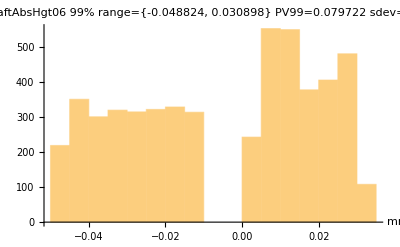

```mathematica
{histFresidplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Add trim FID data section here if necessary

Now fit a plane surface to the FID points

```mathematica
fitbasisR={1,x,y};fitidxR="1,1";
fitordR$=StringTake[ToString[fitbasisR],{2,-2}]
```

1, x, y

```mathematica
rFID[x_,y_]=Fit[FIDpts,fitbasisR,{x,y}]
```

0.0193953-0.000586533 x+0.0000781922 y

```mathematica
vp1={0.5,-5,.5};
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
refplt=Plot3D[rFID[x,y],{x,xminUR,xmaxUR},{y,yminUR,ymaxUR},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.5],AxesLabel->{"Xval","Yval",""},ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

```mathematica
rFID[x,y]/.x->14/.y->41
```

0.0143897

```mathematica
rFID[x,y]/.x->100/.y->41
```

-0.0360522

FID surface is Tilted down by 50 microns from LL to LR in OGP coords

Subtract the fit from the FID points to look at residual stats.

```mathematica
FIDcorrected=Table[{FIDpts[[i,1]],FIDpts[[i,2]],FIDpts[[i,3]]-rFID[FIDpts[[i,1]],FIDpts[[i,2]]]}
,{i,1,Length[FIDpts]}
];
```

```mathematica
reflen$=ToString[Length[FIDcorrected]]
```

5190

```mathematica
FIDresidsPlt=ListPointPlot3D[FIDcorrected,PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval","Z[µm]"},PlotLabel->fileinS<>"\nThis shows FID after subt plane fit"]
```

-Graphics3D-

```mathematica
Button["Export FIDresids plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_FIDresids.tiff",FIDresidsPlt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export FIDresids plot

```mathematica
zFIDresids=Take[FIDcorrected,All,{3}]//Flatten;
```

Look at quality of FID plane correction to FID points:

```mathematica
maxzR2=Max[zFIDresids];minzR2=Min[zFIDresids];sigmaR2=StandardDeviation[zFIDresids];
zbinR2=BinCounts[zFIDresids,(maxzR2-minzR2)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrange99=hrange[zFIDresids,0.005,0.995];
PVrange99=hgtrange99[[2]]-hgtrange99[[1]];
sigmaR2//NumberForm[#,5]&
```

0.0011763

```mathematica
histFIDresidplt=Histogram[zFIDresids,50,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileinS<>" FIDresids"<>"\n99%="<>ToString[hrange[zFIDresids,0.005,0.995]//NumberForm[#,4]&]<>", PV99="<>ToString[PVrange99//NumberForm[#,4]&]<>"\nsdev="<>ToString[sigmaR2//NumberForm[#,4]&]<>zunit$];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

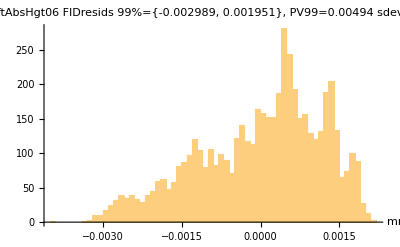

```mathematica
{histFIDresidplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
Button["Export FID resids histogram plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_FIDhist.tiff",histFIDresidplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export FID resids histogram plot

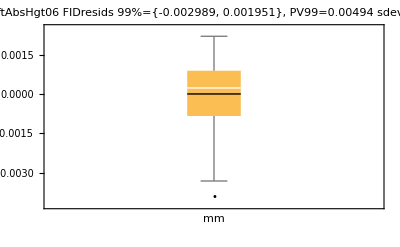

```mathematica
rbwc=BoxWhiskerChart[zFIDresids,{"Outliers",{"MeanMarker",1.0,Thick}},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],PlotLabel->fileinS<>" FIDresids"<>"\n99%="<>ToString[hrange[zFIDresids,0.005,0.995]//NumberForm[#,4]&]<>", PV99="<>ToString[PVrange99//NumberForm[#,4]&]<>"\nsdev="<>ToString[sigmaR2//NumberForm[#,4]&]<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export FID box whisker chart file",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_FIDboxwhisk.tiff",rbwc,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export FID box whisker chart file

```mathematica
vp1={-2,-2,1.5};
```

## Now work on RAFT pts. Need to clean up the points before fitting. Need to leave points in absolute coords: do not convert to residuals for fitting the final surface equation.

### Return here for next trim iteration on RAFTpts.

```mathematica
Length[RAFTpts]
```

7818

```mathematica
xvalsR=Take[RAFTpts,All,{1}]//Flatten;
yvalsR=Take[RAFTpts,All,{2}]//Flatten;
zvalsR=Take[RAFTpts,All,{3}]//Flatten;
```

```mathematica
xrangeR={xminR=Min[xvalsR],xmaxR=Max[xvalsR]}//N
yrangeR={yminR=Min[yvalsR],ymaxR=Max[yvalsR]}//N
zrangeR={zminR=Min[zvalsR],zmaxR=Max[zvalsR],Mean[zvalsR],StandardDeviation[zvalsR]}//N
```

{4.39235,106.767}

{35.3193,160.858}

{-0.151706,0.431569,0.399336,0.0195974}

#### Clean up RAFT points, removing outliers. MUST EXECUTE THIS SECTION.

```mathematica
fitbasis={1,x,y};fitidx="1,1";
fitord$=StringTake[ToString[fitbasis],{2,-2}]
```

1, x, y

```mathematica
RAFTfit[x_,y_]=Fit[RAFTpts,fitbasis,{x,y}]
```

0.41094-0.000472186 x+0.000151676 y

```mathematica
vp1={0.5,-5,.5};
```

```mathematica
RAFTfitplt=Plot3D[RAFTfit[x,y],{x,xminR,xmaxR},{y,yminR,ymaxR},PlotLabel->"RAFTfit="<>TS[RAFTfit[x,y]],AxesLabel->{"X","Y","Z"},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

```mathematica
RAFTfit[x,y]/.x->14/.y->41
```

0.410548

```mathematica
RAFTfit[x,y]/.x->100/.y->41
```

0.36994

See that raw raft surface is tilted by almost the same amount as the FID plane

```mathematica
RAFTandFITplane=Show[lpp01,RAFTfitplt,PlotRange->All,ViewPoint->Dynamic[vp1],PlotLabel->fileinS<>"\nPlane fit to trimmed RAFT points"]
```

-Graphics3D-

```mathematica
Dynamic[vp1]
```

#### Now trim outliers more than some value away fom the fit plane value. First subtract plane fit to the full RAFT data. NEW VERSION for flatness stats

```mathematica
RAFTresids=Table[{RAFTpts[[i,1]],RAFTpts[[i,2]],RAFTpts[[i,3]]-RAFTfit[RAFTpts[[i,1]],RAFTpts[[i,2]]]},{i,Length[RAFTpts]}];
Length[RAFTresids]
```

7818

```mathematica
RAFTresidsZ=RAFTresids[[All,{3}]]//Flatten; (*extract the z-values*)
```

```mathematica
{Mean[RAFTresidsZ],Median[RAFTresidsZ],sdRFT=StandardDeviation[RAFTresidsZ]}
```

{-2.88828×10^-16,0.00048092,0.0122807}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

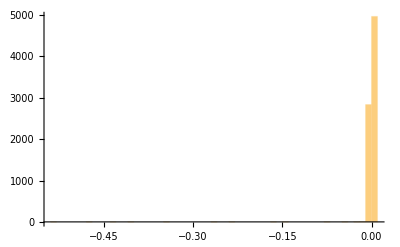

```mathematica
raftflathist=Histogram[RAFTresidsZ,50](*These are the residuals after removing plane fit*)
```

Trim the outliers here. Set the limits to the [0.01,0.995] range each iteration.

```mathematica
medz=Median[RAFTresidsZ]
```

0.00048092

```mathematica
Quantile[RAFTresidsZ,{0.01,0.995}]
```

{-0.00183558,0.0025174}

```mathematica
{threshmin,threshmax}=Input["Enter {min,max} threshold values for trimming bad points.",Quantile[RAFTresidsZ,{0.01,0.995}]]
```

{-0.00183558,0.0025174}

Trim both the XYZ and the Z data lists

```mathematica
RAFTresidsZtrim=
Drop[
Reap[ 
Do[
If[
RAFTpts[[i,3]]-RAFTfit[RAFTpts[[i,1]],RAFTpts[[i,2]]]<threshmax && RAFTpts[[i,3]]-RAFTfit[RAFTpts[[i,1]],RAFTpts[[i,2]]]>threshmin,
Sow[RAFTpts[[i,3]]-RAFTfit[RAFTpts[[i,1]],RAFTpts[[i,2]] ]]
],
{i,Length[RAFTpts]}
]
],
1]//Flatten[#,2]&;
```

```mathematica
RAFTresidsZtrim[[1;;10]]
```

{-0.00182532,-0.00177619,-0.00175276,-0.00172862,-0.00176148,-0.00168234,-0.00182051,-0.00171736,-0.00159722,-0.00157608}

```mathematica
RAFTdatatrim=
Drop[
Reap[
 Do[
If[
RAFTpts[[i,3]]-RAFTfit[RAFTpts[[i,1]],RAFTpts[[i,2]]]<threshmax && RAFTpts[[i,3]]-RAFTfit[RAFTpts[[i,1]],RAFTpts[[i,2]]]>threshmin,Sow[RAFTpts[[i]]]
],
{i,Length[RAFTpts]}]
],
1]//Flatten[#,2]&;
```

```mathematica
RAFTresidsXYZtrim=Table[{RAFTdatatrim[[i,1]],RAFTdatatrim[[i,2]],RAFTresidsZtrim[[i]]},{i,Length[RAFTdatatrim]}];
```

Use these RAFT zresids for Flatness statistics. This excludes tilt effects and only looks at intrinsic surface flatness.

```mathematica
quantlist=Reverse[{0.0,0.005,0.01,0.025,0.25,0.50,0.75,0.975,0.99,0.995,1.0}];
```

```mathematica
qresRFT=Quantile[RAFTresidsZtrim,quantlist];
```

```mathematica
qtableRFT=Transpose[{quantlist,qresRFT}];
%//TableForm
```

1. | 0.00251221
0.995 | 0.00237342
0.99 | 0.0023031
0.975 | 0.00213541
0.75 | 0.00117312
0.5 | 0.00048968
0.25 | -0.000338273
0.025 | -0.00142159
0.01 | -0.0016308
0.005 | -0.00170772
0. | -0.00183307

```mathematica
Button["Export Flatness Quantile table file",Export[fileinS<>"_"<>"_RAFTflatQuantiles.xlsx",Prepend[qtableRFT,{fileinS<>", RAFT flatness Quantiles"}],"XLSX"]]
```

Export Flatness Quantile table file

```mathematica
maxzRFT=Max[RAFTresidsZtrim];minzRFT=Min[RAFTresidsZtrim];sigmaRFT=StandardDeviation[RAFTresidsZtrim];
zbinRFT=BinCounts[RAFTresidsZtrim,sdRFT/3];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrangeRFT95=hrange[RAFTresidsZtrim,0.025,0.975];
PVrangeRFT95=hgtrangeRFT95[[2]]-hgtrangeRFT95[[1]];
hgtrangeRFT99=hrange[RAFTresidsZtrim,0.005,0.995];PVrangeRFT99=hgtrangeRFT99[[2]]-hgtrangeRFT99[[1]];
sigmaRFT//NumberForm[#,5]&;
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
raftflatplt=ListPointPlot3D[RAFTresidsXYZtrim,PlotRange->All,ViewPoint->Dynamic[vp1],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval","Z [µm]"},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],PlotLabel->fileinS<>": RAFT flatness"<>"\n95%range="<>ToString[hgtrangeRFT95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeRFT95[[2]]-hgtrangeRFT95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeRFT99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeRFT99[[2]]-hgtrangeRFT99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sdRFT//NumberForm[#,3]&]<>zunit$]
```

-Graphics3D-

```mathematica
Dynamic[vp1]
```

```mathematica
Button["Export RAFT Flatness plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>raftlen$<>"_RAFTflat.tiff",raftflatplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export RAFT Flatness plot

```mathematica
zrangeR
```

{-0.151706,0.431569,0.399336,0.0195974}

Need integer for number of bins, so need to Round.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

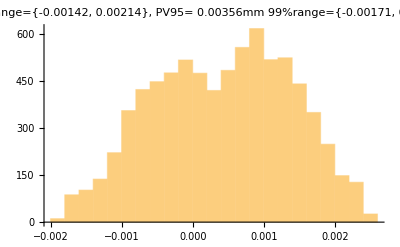

```mathematica
raftflathist=Histogram[RAFTresidsZtrim,50(maxzRFT-minzRFT)/sdRFT//Round[#]&,PlotLabel->fileinS<>": RAFT flatness"<>"\n95%range="<>ToString[hgtrangeRFT95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeRFT95[[2]]-hgtrangeRFT95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeRFT99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeRFT99[[2]]-hgtrangeRFT99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sdRFT//NumberForm[#,3]&]<>zunit$](*These are the residuals after removing plane fit*)
```

```mathematica
Button["Export RAFT Flatness histogram",Export[ToString[StringDrop[fileinS,0]]<>"_"<>raftlen$<>"_RAFTflatHist.tiff",raftflathist,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export RAFT Flatness histogram

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

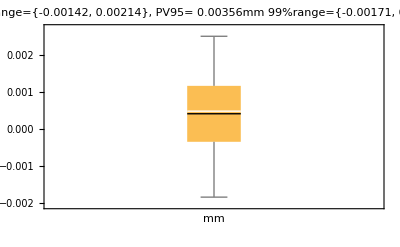

```mathematica
sbwcRFT=BoxWhiskerChart[RAFTresidsZtrim,{"Outliers",{"MeanMarker",1.0,Thick}},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],PlotLabel->fileinS<>": RAFT flatness"<>"\n95%range="<>ToString[hgtrangeRFT95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeRFT95[[2]]-hgtrangeRFT95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeRFT99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeRFT99[[2]]-hgtrangeRFT99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sdRFT//NumberForm[#,3]&]<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export Flatness whisker chart file",Export[ToString[StringDrop[fileinS,0]]<>"_"<>"_RAFTflatBoxWhsk.tiff",sbwcRFT,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export Flatness whisker chart file

```mathematica
Button["Export XYZ flatness height data.",Export[fileinS<>"_RAFTflat.xlsx",RAFTresidsXYZtrim,"XLSX"]]
```

Export XYZ flatness height data.

```mathematica
strimplt=ListPointPlot3D[RAFTdatatrim,PlotRange->All,ViewPoint->Dynamic[vp1],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>": RAFT trimmed"]
```

-Graphics3D-

```mathematica
raftlen$=ToString[Length[RAFTdatatrim]]
```

7699

```mathematica
Button["Export trimmed RAFT region plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>raftlen$<>"_RAFTtrim.tiff",strimplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export trimmed RAFT region plot

```mathematica
qtableRFT
```

{{1.,0.00251221},{0.995,0.00237342},{0.99,0.0023031},{0.975,0.00213541},{0.75,0.00117312},{0.5,0.00048968},{0.25,-0.000338273},{0.025,-0.00142159},{0.01,-0.0016308},{0.005,-0.00170772},{0.,-0.00183307}}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Click to iterate RAFTpts trim",RAFTpts=RAFTdatatrim;NotebookLocate["Iterate RAFTpts trim"]]
```

Click to iterate RAFTpts trim

```mathematica
Length[RAFTpts]
```

7818

```mathematica
Length[RAFTdatatrim]
```

7699

## Set RAFTpts to the trimmed array. Continue from here when desired trim above is achieved.

```mathematica
If[Length[RAFTdatatrim]<Length[RAFTpts],RAFTpts=RAFTdatatrim;Print["Set trim data to RAFTpts array."],Print["Both arrays are the same. Nothing to change."]]
```

Set trim data to RAFTpts array.

Now fit plane to remaining resids

```mathematica
fitbasis={1,x,y};fitidx="1,1";
fitord$=StringTake[ToString[fitbasis],{2,-2}]
```

1, x, y

```mathematica
RAFTfittrim[x_,y_]=Fit[RAFTpts,fitbasis,{x,y}]
```

0.408529-0.000450646 x+0.000168133 y

```mathematica
vp1={0.5,-5,.5};
```

```mathematica
RAFTfitplt=Plot3D[RAFTfittrim[x,y],{x,xminR,xmaxR},{y,yminR,ymaxR},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]];
```

```mathematica
RAFTfitpltPts=Show[strimplt,RAFTfitplt]
```

-Graphics3D-

```mathematica
Button["Export trimmed RAFT region plot with pts",Export[ToString[StringDrop[fileinS,0]]<>"_"<>raftlen$<>"_RAFTptsPlane.tiff",RAFTfitpltPts,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export trimmed RAFT region plot with pts

```mathematica
rFID[x,y]
```

0.0193953-0.000586533 x+0.0000781922 y

Subtract FID expression from the Raft to get the expression of the raft relative to the FID.

```mathematica
RAFTtoFID[x_,y_]=RAFTfittrim[x,y]-rFID[x,y]
```

0.389133+0.000135887 x+0.000089941 y

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Raft2FIDplt=Plot3D[RAFTtoFID[x,y],{x,xminR,xmaxR},{y,yminR,ymaxR},ColorFunction->"Rainbow",ImageSize->400,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

## Input the Cal run DatumEqns expressions from one of the Calibration runs prior to the raft measurement. Keep time between measurements short.

```mathematica
Clear[cDatum,cFID,cDATUMtocFID]
```

```mathematica
calfile=Input["Enter path to cal run DatumEqns.txt file",calfile]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150224/MF03CalRun05_files/MF03CalRun05DatumEqns.txt

```mathematica
caldata=Import[calfile,{"Lines"}];
```

```mathematica
caldata//TableForm
```

MF03CalRun05
cDatum[x,y]= -29.40316343697158 - 0.0004472672189521383*x + 0.00015911680444565538*y
cFID[x,y] = 0.020392594745722078 - 0.0005837929129679135*x + 0.00007918172130497194*y
cDATUMtocFID[x,y] = -29.423556031717304 + 0.00013652569401577516*x + 0.00007993508314068344*y
nomRaftSurfFit[x,y] = 0.4084134311235711 - 0.0002951743450431775*x + 0.00009097410021058794*y

```mathematica
cDatum[x_,y_]=ToExpression[caldata[[2]]]
cFID[x_,y_]=ToExpression[caldata[[3]]]
cDATUMtocFID[x_,y_]=ToExpression[caldata[[4]]]
calfilename=caldata[[1]];
```

-29.4032-0.000447267 x+0.000159117 y

0.0203926-0.000583793 x+0.0000791817 y

-29.4236+0.000136526 x+0.0000799351 y

```mathematica
(*<<"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150220/meandatumseqn.txt"*)
```

```mathematica
(*cDatum[x_,y_]=%*)
```

```mathematica
cDatum[50,100]
```

-29.4096

Plot the datum plane relative to the FID plane for the cal file.

```mathematica
Plot3D[cDatum[x,y],{x,xminR,xmaxR},{y,yminR,ymaxR},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->calfilename<>"\ncDatum",PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

```mathematica
Datum2FIDplt=Plot3D[cDATUMtocFID[x,y]+29.81,{x,xminR,xmaxR},{y,yminR,ymaxR},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->calfilename<>"\nDatum to FID plot",PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

Plot both the Raft and Datum surfaces relative to the FID plane.

```mathematica
Show[Datum2FIDplt,Raft2FIDplt,PlotLabel->filein<>", "<>calfilename]
```

-Graphics3D-

Plot the difference between the 2 FID planes to make sure they look right.

```mathematica
Plot3D[cFID[x,y]-rFID[x,y],{x,xminR,xmaxR},{y,yminR,ymaxR},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

Plot the Raft relative to the Datum without the FID corrections.

```mathematica
Plot3D[RAFTfittrim[x,y]-cDatum[x,y],{x,xminR,xmaxR},{y,yminR,ymaxR},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

Now compute the difference between the Datum plane and the Raft, removing the FID.

```mathematica
Raft2Datum[x_,y_]=RAFTtoFID[x,y]-cDATUMtocFID[x,y]
```

29.8127-6.38263×10^-7 x+0.0000100059 y

```mathematica
{xminR,xmaxR,yminR,ymaxR}
```

{4.39235,106.767,35.3193,160.858}

```mathematica
AbsRaftHgt=Plot3D[Raft2Datum[x,y],{x,xminR,xmaxR},{y,yminR,ymaxR},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

Plot the nominal DatumA plane wrt 3ball datum system.

```mathematica
DatumAplane=Plot3D[29.81,{x,xminR,xmaxR},{y,yminR,ymaxR},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]];
```

Finally, show the measured raft plane relative to the nominal. The design value is 29.81mm.

```mathematica
filein
```

150224RaftAbsHgt06

```mathematica
RAFTabshgtplt=Show[AbsRaftHgt,DatumAplane,PlotLabel->filein<>", "<>calfilename,ViewPoint->Front]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
(*Button["Export fit RAFT abs hgt plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>raftlen$<>"_RAFTabshgt.tiff",RAFTabshgtplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]*)
```

#### Input OGP MM Ball fit coord data txt file. This is the output from the File->Print/Edit menu item that is saved after one of the MF03 ball cal runs. Compute raft corner points relative to the LL bal center.

Bypass this input for nominal points.

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150224/Run2.txt"
```

```mathematica
ballfile=Input["Enter path to BallFitResult file",ballfile]
```

```mathematica
balldata=Import[ballfile,"List"];
```

```mathematica
balldata
```

```mathematica
ToExpression[ImportString[balldata[[-3]],"Words"]][[3;;5]]
```

```mathematica
ballLL=ToExpression[ImportString[balldata[[-3]],"Words"]][[3;;5]];ballLR=ToExpression[ImportString[balldata[[-2]],"Words"]][[3;;5]];ballUC=ToExpression[ImportString[balldata[[-1]],"Words"]][[3;;5]];
```

```mathematica
{{xminR,xmaxR},{yminR,ymaxR}}
```

Compute nominal ball locations as offsets from the LL ball center. Use dimensions from raft baseplate drawing LCA-10212.

```mathematica
ballLL={14.372,41.520,-29.40}
ballLR=ballLL+{86.5,0,0}
ballUC=ballLL+{43.25,113.5,0}
raftcorneroffset={(126.5/2)-43.25,6.5,-29.81};
```

{14.372,41.52,-29.4}

{100.872,41.52,-29.4}

{57.622,155.02,-29.4}

Raft LL corner is {-20,-6.5} from LL ball center. Compute corner locations as offsets from the LL corner

```mathematica
ballLL[[1;;3]]
```

{14.372,41.52,-29.4}

```mathematica
raftLL=ballLL-{20,-6.5,0}
raftUR=raftLL+{126.5,126.5,0}
raftLR=raftLL+{126.5,0,0}
raftUL=raftLL+{0,126.5,0}
```

{-5.628,48.02,-29.4}

{120.872,174.52,-29.4}

{120.872,48.02,-29.4}

{-5.628,174.52,-29.4}

```mathematica
raftregion=Rectangle[raftLL[[1;;2]],raftUR[[1;;2]]]
```

Rectangle[{-5.628,48.02},{120.872,174.52}]

Compute height at corner points. The PV raft height is the difference between the extgrema of these corners.

```mathematica
PVmax=FindMaximum[{Raft2Datum[x,y],{x,y}∈raftregion},{x,y}][[1]]
```

29.8131

```mathematica
PVmin=FindMinimum[{Raft2Datum[x,y],{x,y}∈raftregion},{x,y}][[1]]
```

29.8131

```mathematica
PVraft=PVmax-PVmin
```

0.00134649

```mathematica
meanrafthgt=Integrate[Raft2Datum[x,y],{x,y}∈raftregion]/Area[raftregion]
```

29.8138

```mathematica
line7="PV raft extrema = "<>TS[PVraft]<>"\nMean raft abs height = "<>TS[meanrafthgt]
```

PV raft extrema = 0.00134649
Mean raft abs height = 29.8138

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
RAFTabshgtpltPV=Show[RAFTabshgtplt,PlotLabel->filein<>", "<>calfilename<>"\nPV raft height = "<>TS[NumberForm[PVraft,3]]<>" at Zmean= "<>TS[NumberForm[meanrafthgt,5]]]
```

-Graphics3D-

```mathematica
Button["Export fit RAFT abs hgt plot",Export[ToString[StringDrop[fileinS,0]]<>"w"<>calfilename<>"_RAFTabshgtPV.tiff",RAFTabshgtpltPV,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export fit RAFT abs hgt plot

```mathematica
RAFTtoFID[x,y]-cDATUMtocFID[x,y]
```

29.8127-6.38263×10^-7 x+0.0000100059 y

### Output result eqns to txt file

```mathematica
eqnfile$=fileinS<>" - "<>StringReplace[calfilename," "->""]
```

150224RaftAbsHgt06 - MF03CalRun05

```mathematica
line1="**Raft data from file: "<>fileinfull;
```

```mathematica
line2="**Ball datum cal datum plane relative to FID is from file: "<>FileNameTake[calfile];
```

```mathematica
line21="cDATUMtocFID[x,y]="<>TS[cDATUMtocFID[x,y]//InputForm]
```

cDATUMtocFID[x,y]=-29.423556031717304 + 0.00013652569401577516*x + 0.00007993508314068344*y

```mathematica
line3="RAFTfit[x,y] = "<>TS[RAFTfittrim[x,y]//InputForm]
```

RAFTfit[x,y] = 0.4085286545881141 - 0.0004506460518464756*x + 0.00016813315170223294*y

```mathematica
line31= "rFIDeqn[x,y] = "<>TS[rFID[x,y]//InputForm]
```

rFIDeqn[x,y] = 0.019395258502078943 - 0.000586533482802734*x + 0.00007819215732098003*y

```mathematica
line32="RAFTtoFID[x,y] = "<>TS[RAFTtoFID[x,y]//InputForm]
```

RAFTtoFID[x,y] = 0.38913339608603514 + 0.00013588743095625837*x + 0.00008994099438125291*y

```mathematica
line5= "**Subtract the Datum to FID eqn from the Raft to FID eqn to get the absolute height of the Raft relative to the 3ball datum:";
```

```mathematica
line6 = "Raft2Datum[x,y] = "<>ToString[Raft2Datum[x,y]//InputForm]
```

Raft2Datum[x,y] = 29.81268942780334 - 6.382630595167861*^-7*x + 0.000010005911240569475*y

```mathematica
$NumberMarks=False
```

False

```mathematica
line7
```

PV raft extrema = 0.00134649
Mean raft abs height = 29.8138

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Output the equation results",
Export[eqnfile$<>"_fiteqns.txt",{eqnfile$<>"_fiteqns.txt",line1,line2,line21,line3,line31,line32,line5,line6,line7}]]
```

Output the equation results

```mathematica
RAFTfit[x,y]
```

```mathematica
FID
```

## Compare Abs Hgt run results. Read in several measurement results and compare. Results go into parent folder

```mathematica
ncal=0;raft2FIDDeqns={};raftfile=.;raftdata=.;
```

Iterate from here to input different datum to fid cal files.  Do not reset above items.

```mathematica
raftfile=Input["Enter path to raft eqn file",raftfile]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150224/150224RaftAbsHgt06_files/150224RaftAbsHgt06 - MF03CalRun05_fiteqns.txt

Set the working directory to the parent run directory. It is 2 levels above the specified file name.

```mathematica
SetDirectory[DirectoryName[raftfile,2]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150224

```mathematica
raftdata=Import[raftfile,{"Lines"}];
%//TableForm
```

150224RaftAbsHgt06 - MF03CalRun05_fiteqns.txt
**Raft data from file: 150224RaftAbsHgt06.DAT
**Ball datum cal datum plane relative to FID is from file: MF03CalRun05DatumEqns.txt
cDATUMtocFID[x,y]=-29.423556031717304 + 0.00013652569401577516*x + 0.00007993508314068344*y
RAFTfit[x,y] = 0.4085286545881141 - 0.0004506460518464756*x + 0.00016813315170223294*y
rFIDeqn[x,y] = 0.019395258502078943 - 0.000586533482802734*x + 0.00007819215732098003*y
RAFTtoFID[x,y] = 0.38913339608603514 + 0.00013588743095625837*x + 0.00008994099438125291*y
**Subtract the Datum to FID eqn from the Raft to FID eqn to get the absolute height of the Raft relative to the 3ball datum:
Raft2Datum[x,y] = 29.81268942780334 - 6.382630595167861*^-7*x + 0.000010005911240569475*y
PV raft extrema = 0.00134649
Mean raft abs height = 29.8138

```mathematica
Raft2Datumline=-3;
```

```mathematica
raftdata[[Raft2Datumline]] (*Take the desired eqn line from the file*)
```

Raft2Datum[x,y] = 29.81268942780334 - 6.382630595167861*^-7*x + 0.000010005911240569475*y

```mathematica
raft2datum[x_,y_]=ToExpression[raftdata[[Raft2Datumline]]];(*Ignore the BEEP*)
raftfilename=raftdata[[1]];
```

```mathematica
raft2datum[x,y]
```

29.8127-6.38263×10^-7 x+0.0000100059 y

```mathematica
FileNameTake[raftfile]
```

150224RaftAbsHgt06 - MF03CalRun05_fiteqns.txt

```mathematica
vp1={-4,-5,2}
```

{-4,-5,2}

```mathematica
eqnplt=Plot3D[raft2datum[x,y],{x,raftLL[[1]],raftLR[[1]]},{y,raftLR[[2]],raftUR[[2]]},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->FileNameTake[raftfile]<>"\nDatum to FID plot",PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

```mathematica
ncal=Input["Enter index number for this cal eqn expression",ncal]
```

3

```mathematica
AppendTo[raft2FIDDeqns,raft2datum[x,y]]
```

{29.8133+2.47347×10^-6 x+7.67884×10^-6 y,29.8129+2.10358×10^-6 x+8.90852×10^-6 y,29.8127-6.38263×10^-7 x+0.0000100059 y}

```mathematica
raft2FIDDeqns//TableForm
```

29.8133+2.47347×10^-6 x+7.67884×10^-6 y
29.8129+2.10358×10^-6 x+8.90852×10^-6 y
29.8127-6.38263×10^-7 x+0.0000100059 y

```mathematica
(*Write the equations set to a temp file*)
raft2FIDDeqns>>"tempAllAbsHgtEqns.m"
```

Compute the mean of all of the input cal eqns and plot them all relative to the mean to see the spread.

```mathematica
meanRaft=Mean[raft2FIDDeqns]//Simplify
```

29.813+1.31293×10^-6 x+8.86442×10^-6 y

```mathematica
parentfolder=FileNameTake[raftfile,{-3}]
```

Runs 150224

```mathematica
RaftAllPlt=Table[Plot3D[raft2FIDDeqns[[i]],{x,raftLL[[1]],raftLR[[1]]},{y,raftLR[[2]],raftUR[[2]]},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->parentfolder<>"\nRaft Abs Hgt",PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]],{i,1,Length[raft2FIDDeqns]}];
```

```mathematica
allraftsplt=Show[RaftAllPlt]
```

-Graphics3D-

```mathematica
Button["Export All Rafts Abs plot",Export[parentfolder<>"_AllRaftsAbsHgt.tiff",allraftsplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export All Rafts Abs plot

```mathematica
residRaftPlt=Table[Plot3D[raft2FIDDeqns[[i]]-meanRaft,{x,raftLL[[1]],raftLR[[1]]},{y,raftLR[[2]],raftUR[[2]]},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->parentfolder<>"\nRaft Abs Hgt plot",PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]],{i,1,Length[raft2FIDDeqns]}];
```

```mathematica
allresidRaftPlts=Show[residRaftPlt,PlotLabel->"Raft heights relative to mean plane"]
```

-Graphics3D-

```mathematica
Button["Export Raft repeatability plot",Export[parentfolder<>"_AllRaftsToMean.tiff",allresidRaftPlts,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export Raft repeatability plot

```mathematica
PVmaxMean=FindMaximum[{meanRaft,{x,y}∈raftregion},{x,y}][[1]]
```

29.8147

```mathematica
PVminMean=FindMinimum[{meanRaft,{x,y}∈raftregion},{x,y}][[1]]
```

29.8134

```mathematica
PVraftMean=PVmaxMean-PVminMean
```

0.00128743

```mathematica
meanmeanrafthgt=Integrate[meanRaft,{x,y}∈raftregion]/Area[raftregion]
```

29.814

```mathematica
meanofall=Plot3D[meanRaft,{x,raftLL[[1]],raftLR[[1]]},{y,raftLR[[2]],raftUR[[2]]},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->parentfolder<>" Mean of All Abs Hgt\nMean Hgt= "<>TS[meanmeanrafthgt]<>" PV= "<>TS[NumberForm[PVraftMean,3]]<>"mm",PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

```mathematica
Button["Export Mean of All plot",Export[parentfolder<>"_AllRaftsMeanAbsHgt.tiff",meanofall,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export Mean of All plot

```mathematica
meanRaft
```

29.813+1.31293×10^-6 x+8.86442×10^-6 y

```mathematica
TS[meanRaft//InputForm]
```

29.812966755153777 + 1.3129287655077742*^-6*x + 8.864422154336026*^-6*y

```mathematica
Button["Output the mean raft results",
Export[parentfolder<>"_AllmeanHgtResults.txt",{parentfolder<>"\nMeanRaft[x,y]= "<>TS[meanRaft//InputForm]<>"\nMean Hgt = "<>TS[meanmeanrafthgt]<>"\nPV of mean raft = "<>TS[PVraftMean]}]]
```

Output the mean raft results